## 134Ce

```mathematica
ClearAll["Global`*"]
```

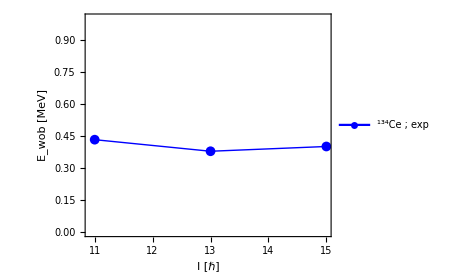

```mathematica
yrastEn=Sort[{8582.9,7580.7,6596.6,5724.5,4907.3,4183.0,3718.96}];
wob1En=Sort[{5716.9,4923.9,4383.8}];
yrastSpin=Table[i,{i,10,22,2}];
wob1Spin=Table[i,{i,11,15,2}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i]]+yrast[[i+1]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{18,Bold,Black},PlotLegends->Placed[{Row[{Superscript["","134"],"Ce ; exp"}]},{0.3,0.9}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/134Ce.pdf",fig];
Show[fig]
```